## Section | Roots versus Radicals

Sometimes there is great utility in having a closed-form expression—and all readers  will be familiar with the general solution to the quadratic equation.

Solve the general quadratic equation:

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

The principal idea lying behind these expressions is the computation of the Discriminant which, for a general polynomial of degree n, is the product over all pairs of roots x_i, x_j of (x_i-x_j)^2.

Compute the Discriminant of the general quadratic equation:

```mathematica
Discriminant[a x^2+b x+c,x]
```

b^2-4 a c

### Closed Forms

One advantage of using the Wolfram Language is that, for many problems in computational physics, one can obtain a closed form solution with associated advantages:

efficient and stable numerical computation

analytical insight, including integration, series expansion, and asymptotic analysis

For example, the antiderivative of ⅇ^(-x^2) is not an elementary function. But that is no obstacle for performing computation.

Compute the integral ∫ⅇ^(-x^2)ⅆx:

```mathematica
∫ⅇ^(-x^2)ⅆx
```

1/2 √π Erf[x]

## Roots of Polynomials

### As Radicals

However, many physicists and engineers have a somewhat unhealthy obsession with “closed-form” expressions. The roots of cubic and quartic polynomials can, of course, be represented using radicals. But should they be?

Compute the roots of x^3+α x+1:

```mathematica
cubicroots=Solve[x^3+α x+1==0,x]
```

{{x→-((2/3)^(1/3) α)/((-9+√3 √(27+4 α^3))^(1/3))+((-9+√3 √(27+4 α^3))^(1/3))/(2^(1/3) 3^(2/3))},{x→((1+ⅈ √3) α)/(2^(2/3) 3^(1/3) (-9+√3 √(27+4 α^3))^(1/3))-((1-ⅈ √3) (-9+√3 √(27+4 α^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{x→((1-ⅈ √3) α)/(2^(2/3) 3^(1/3) (-9+√3 √(27+4 α^3))^(1/3))-((1+ⅈ √3) (-9+√3 √(27+4 α^3))^(1/3))/(2 2^(1/3) 3^(2/3))}}

The roots of this irreducible cubic are all real for α=-2. However, this is not obvious from the explicit solution:

```mathematica
cubicroots/.α->-2
```

{{x→(1/2 (-9+ⅈ √15))^(1/3)/3^(2/3)+2/(3/2 (-9+ⅈ √15))^(1/3)},{x→-((1-ⅈ √3) (1/2 (-9+ⅈ √15))^(1/3))/(2 3^(2/3))-(1+ⅈ √3)/(3/2 (-9+ⅈ √15))^(1/3)},{x→-((1+ⅈ √3) (1/2 (-9+ⅈ √15))^(1/3))/(2 3^(2/3))-(1-ⅈ √3)/(3/2 (-9+ⅈ √15))^(1/3)}}

Small numeric error from round-off gives small imaginary parts:

```mathematica
N[%,20]
```

{{x→1.+0. ⅈ},{x→-1.6180339887498948482+0. ⅈ},{x→0.6180339887498948482+0. ⅈ}}

The small imaginary parts can be eliminated using Chop:

```mathematica
Chop@%
```

{{x→1.},{x→-1.6180339887498948482},{x→0.6180339887498948482}}

As expected, the irreducible cubic factors for α=-2:

```mathematica
Factor[x^3-2 x+1]
```

(-1+x) (-1+x+x^2)

Including an appropriate Extension full factorization is possible:

```mathematica
Factor[x^3-2 x+1,Extension->√5]
```

-1/4 (-1+√5-2 x) (-1+x) (1+√5+2 x)

Alternatively, in this case, one can obtain the roots directly:

```mathematica
cubicroots/.α->-2//FullSimplify
```

{{x→1},{x→1/2 (-1-√5)},{x→2/(1+√5)}}

### As Root Objects

While an explicit form may be useful in some cases, it is nearly always better to express the roots as Root objects—a concise way of expressing algebraic numbers via the minimal polynomial they satisfy, along with a canonical ordering in the complex plane (specified by the second argument of Root).

Using Reduce the roots of cubic and quartic polynomials are automatically represented as Root objects:

```mathematica
exactcubicroots=Reduce[x^3+α x+1==0,x]
```

x==Root[1+α #1+#1^3&,1]||x==Root[1+α #1+#1^3&,2]||x==Root[1+α #1+#1^3&,3]

These reduce to simple expressions  when α->-2:

```mathematica
exactcubicroots/.α->-2
```

x==1/2 (-1-√5)||x==1/2 (-1+√5)||x==1

If all the polynomial coefficients are numerical, then an explicit approximation is returned, which can be evaluated to arbitrary precision:

```mathematica
Reduce[x^3+√3 x+1==0,x]
```

x==||x==||x==

To get a radical form, you can use ToRadicals:

```mathematica
ToRadicals[%]
```

x==-(2/(-3+√(9+4 √3)))^(1/3)/3^(1/6)+(1/6 (-3+√(9+4 √3)))^(1/3)||x==-1/2 (1+ⅈ √3) (1/6 (-3+√(9+4 √3)))^(1/3)+(1-ⅈ √3)/(2^(2/3) 3^(1/6) (-3+√(9+4 √3))^(1/3))||x==-1/2 (1-ⅈ √3) (1/6 (-3+√(9+4 √3)))^(1/3)+(1+ⅈ √3)/(2^(2/3) 3^(1/6) (-3+√(9+4 √3))^(1/3))

This output is more complicated—and less useful—than the Root form.

## Which Form is Better?

In addition to size, there are many reasons to prefer the Root form over a radical expression:

It is typically faster to obtain.

It is numerically more stable to evaluate. In general, radical formulations are prone to numeric problems. Root objects do not have this liability.

When the roots of an irreducible cubic are all real, but not rational, the so-called “casus irreducibilis” shows that they still must be expressed in terms of ⅈ (see mathworld.wolfram.com/CasusIrreducibilis.html). This means that numeric evaluation will give small imaginary parts unless, by happenstance, they exactly cancel. Small numeric error from round off makes this unlikely.

For sufficiently complicated algebraics, it is often faster to evaluate the Root form numerically, at least at high precision.

Symmetric polynomial combinations of Root objects simplify using RootReduce.

For applications in mathematics (e.g. Vieta jumping in number theory), engineering or physics one usually works with combinations of roots (e.g. applications of Routh-Hurwitz integrals) so Vieta's formulas relating the coefficients of a polynomial to sums and products of its roots is much more useful than explicit values for the roots.

Derivatives of Root objects with respect to a parameter are expressed in terms of Root objects. This is useful for eigenvalue sensitivity analysis.

For higher-order irreducible polynomials, radical representations do not exist in general. However, there are generalized hypergeometric representations (see Trott and Adamchik’s quintic poster and the example below).

One can sometimes avoid the Root form by using ToRadicals—but for all practical computation, you are better off working with Root objects.

### Examples

#### Derivatives

Compute the derivative of (the first root of) x^7-x+α with respect to the parameter α:

```mathematica
D[Root[x↦x^7-x+α,1], α]
```

-1/(-1+7 Root[α-#1+#1^7&,1]^6)

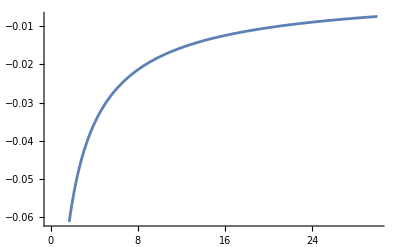

```mathematica
Plot[%,{α,0,30}]
```

#### Series Expansion

It is also easy to compute series expansions of Root objects.

Expand each of the three roots of x^3-x+α==0 as a series in α:

```mathematica
root[1]=Root[x↦x^3-x+α,1]+O[α]^7
```

-1-α/2+(3 α^2)/8-α^3/2+(105 α^4)/128-(3 α^5)/2+(3003 α^6)/1024+O[α]^7

```mathematica
root[2]=Root[x↦x^3-x+α,2]+O[α]^7
```

α+α^3+3 α^5+O[α]^7

```mathematica
root[3]=Root[x↦x^3-x+α,3]+O[α]^7
```

1-α/2-(3 α^2)/8-α^3/2-(105 α^4)/128-(3 α^5)/2-(3003 α^6)/1024+O[α]^7

The sum of these three roots vanishes up to this order as is expected since the coefficient of x^2 is zero:

```mathematica
root[1]+root[2]+root[3]
```

O[α]^7

#### Hypergeometric Representations

Solve the quintic x^5-x-α==0:

```mathematica
quintic=Solve[x^5-x-α==0,x]
```

{{x→Root[-α-#1+#1^5&,1]},{x→Root[-α-#1+#1^5&,2]},{x→Root[-α-#1+#1^5&,3]},{x→Root[-α-#1+#1^5&,4]},{x→Root[-α-#1+#1^5&,5]}}

Radical representations for higher-order irreducible polynomials do not exist in general.

Use ToRadicals to attempt to express these Root objects as radicals:

```mathematica
ToRadicals[quintic]
```

{{x→Root[-α-#1+#1^5&,1]},{x→Root[-α-#1+#1^5&,2]},{x→Root[-α-#1+#1^5&,3]},{x→Root[-α-#1+#1^5&,4]},{x→Root[-α-#1+#1^5&,5]}}

However, there are generalized hypergeometric representations (see Trott and Adamchik’s quintic poster).

Compute the series expansion (of the second root) directly:

```mathematica
root[2]=Root[x↦x^5-x-α,2]+O[α]^45
```

-α-α^5-5 α^9-35 α^13-285 α^17-2530 α^21-23751 α^25-231880 α^29-2330445 α^33-23950355 α^37-250543370 α^41+O[α]^45

Determine the coefficients:

```mathematica
coefs=CoefficientList[root[2],α]
```

{0,-1,0,0,0,-1,0,0,0,-5,0,0,0,-35,0,0,0,-285,0,0,0,-2530,0,0,0,-23751,0,0,0,-231880,0,0,0,-2330445,0,0,0,-23950355,0,0,0,-250543370}

Find a sequence that generates these coefficients using FindSequenceFunction:

```mathematica
c[n_]=FindSequenceFunction[coefs,n]
```

-((5^(-5/2+(5 n)/4) (1+(-1)^n-2 Cos[(n π)/2]) Gamma[-3/10+n/4] Gamma[-1/10+n/4] Gamma[1/10+n/4] Gamma[3/10+n/4])/(4 Gamma[1/5] Gamma[2/5] Gamma[3/5] Gamma[4/5] Gamma[n]))

Re-sum the series to find an explicit (generalized hypergeometric or HypergeometricPFQ) representation of one of the roots, noting that the first term in the sequence corresponds to n==1:

```mathematica
r[α_]=∑_(n=1)^∞ c[n] α^(n-1)
```

-α HypergeometricPFQ[{1/5,2/5,3/5,4/5},{1/2,3/4,5/4},(3125 α^4)/256]

Check this result by series expansion:

```mathematica
r[α]+O[α]^45
```

-α-α^5-5 α^9-35 α^13-285 α^17-2530 α^21-23751 α^25-231880 α^29-2330445 α^33-23950355 α^37-250543370 α^41+O[α]^45

Compute the second root of x^5-x+1/2 numerically:

```mathematica
N[Root[x↦x^5-x+1/2,2],45]
```

0.550606579334134968304020582185202073666608482

Compare with the hypergeometric representation:

```mathematica
%==r[-1/2]
```

True

More generally, the following family of hypergeometric functions have very simple minimal polynomials:

```mathematica
Table[{n,hyper=HypergeometricPFQ[Range[n-1]/n,Join[{n},Range[2,n-2]]/(n-1),n^n/(1-n)^(n-1)],MinimalPolynomial[RootApproximant@hyper][x]},{n,3,9}]
```

(3 | (2 sin(1/3 sin^-1((3 √3)/2)))/(√3) | x^3-x+1
4 | _3 F_2(1/4,1/2,3/4;2/3,4/3;-256/27) | x^4+x-1
5 | _4 F_3(1/5,2/5,3/5,4/5;1/2,3/4,5/4;3125/256) | x^5-x+1
6 | _5 F_4(1/6,1/3,1/2,2/3,5/6;2/5,3/5,4/5,6/5;-46656/3125) | x^6+x-1
7 | _6 F_5(1/7,2/7,3/7,4/7,5/7,6/7;1/3,1/2,2/3,5/6,7/6;823543/46656) | x^7-x+1
8 | _7 F_6(1/8,1/4,3/8,1/2,5/8,3/4,7/8;2/7,3/7,4/7,5/7,6/7,8/7;-16777216/823543) | x^8+x-1
9 | _8 F_7(1/9,2/9,1/3,4/9,5/9,2/3,7/9,8/9;1/4,3/8,1/2,5/8,3/4,7/8,9/8;387420489/16777216) | x^9-x+1)

## Transcendental Roots

In general, the implicit exact roots of transcendental equations can also expressed as Root objects.

Plot 0x+0x for 0<=x<=20:

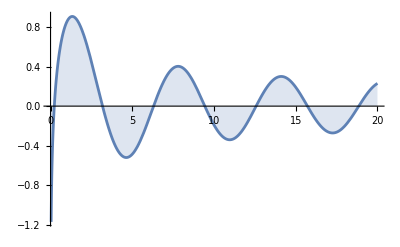

```mathematica
Plot[BesselJ[0,x]+BesselY[0,x]==0,{x,0,20},Filling->Axis]
```

Solve for the exact roots of 0x+0x==0 for 0<=x<=20:

```mathematica
Solve[{BesselJ[0,x]+BesselY[0,x]==0,0<=x<=20},x]
```

Solve::incs: Warning: Solve was unable to prove that the solution set found is complete.

{{x→},{x→},{x→},{x→},{x→},{x→},{x→}}

Verify the first root exactly:

```mathematica
BesselJ[0,x]+BesselY[0,x]==0/.x->//FullSimplify
```

True

This computation is exact because, internally, the Root object also stores the function that the root satisfies.

Use InputForm to see the internal form of a Root object:

```mathematica
//InputForm
```

Root[{BesselJ[0, #1] + BesselY[0, #1] & , 0.23033\
0781153665990062542718654510676547792163685476144\
3858`30.102999566398122}]

Evaluate the first root to 200 decimal places:

```mathematica
N[x->,200]
```

x→0.23033078115366599006254271865451067654779216368547614438585140180013505710527122551538124823812830978045947459795267052254315566205927126802053185894846591972425086117244444807447028400991451344459099

Verify this root numerically:

```mathematica
BesselJ[0,x]+BesselY[0,x]/.%
```

0.

### References

Timothy Chow’s article What is a closed-form number? is relevant when solving transcendental equations